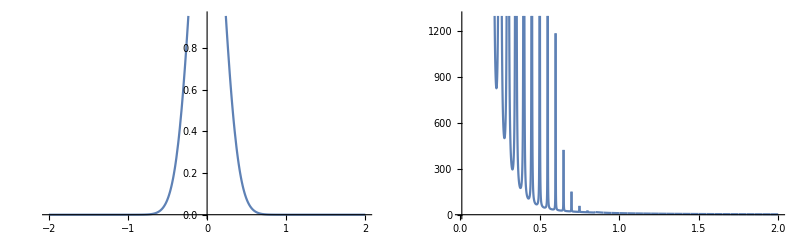

```mathematica
widths=Range[12.5,14,1.5];
response[e_]:=Sum[Exp[-widths[[i]] e^2],{i,1,Length[widths]}]
kernel[e_,s_]:=1/((e-s) (e-Conjugate[s]))
Subscript[σ, i]=0.2;
de=0.05;
emax=5;
tgrid=Range[0,emax,de];
trafo[sr_]:=Re[Sum[response[tgrid[[j]]] kernel[tgrid[[j]],sr],{j,1,Length[tgrid]}]]

bnd=2;
P1=Plot[response[e],{e,-bnd,bnd}];
P2[si_]:=Plot[trafo[x+si],{x,0.01,bnd}];
GraphicsGrid[{{P1,P2[Subscript[σ, i]]}}]
```

```mathematica
si=0.5;
Animate[Plot[kernel[e,sr-I si],{e,1,10}],{sr,1,6,0.1},AnimationRunning->False]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[0.0170507 ⅇ^(-1.20272 (-«18»+x)^2)+0.0176041 ⅇ^(-«19»«1»«1»)+«6»+«20» «1»+0.0752592 ⅇ^(-0.03539 («1»)^2)]

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[0.35463 ⅇ^(-0.168041 x^2)+«10»+0.59498 ⅇ^(-0.0463064 x^2)]

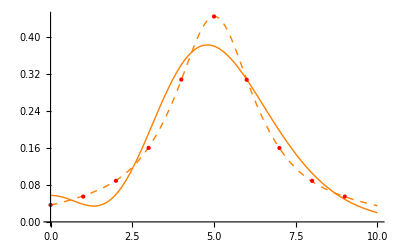

```mathematica
emin=0.001;emax=10;gaussdim=10;
Phi[α_,x_,xi_,c_]:=(c E^(-Abs[α] (x-xi)^2/2));
Phi2[α_,x_,c_]:=(c E^(-Abs[α] x^2/2));

model2=Sum[Phi[a@i,x,xx@i,c@i],{i,gaussdim}];
model3=Sum[Phi2[a@i,x,c@i],{i,gaussdim}];

Data=Table[{e,1/((e-5)^2+1.5^2)},{e,emin,emax}];

nlm2=NonlinearModelFit[Data,model2,Flatten[Table[{{a@i,0.3},{xx@i,3},{c@i,3}},{i,gaussdim}],1],x]
nlm3=NonlinearModelFit[Data,model3,Flatten[Table[{{a@i,0.3},{c@i,-0.3^i}},{i,gaussdim}],1],x]
Show[Plot[nlm2[x],{x,emin,emax},Epilog:>{Red,PointSize[Medium],Point[Data]},PlotStyle->{Orange,Dashed,Thick}],Plot[nlm3[x],{x,emin,emax},PlotStyle->{Orange,Thick},PlotRange->{0,0.6}]]
```

```mathematica
kernel[e_,s_]:=1/((e-s) (e-Conjugate[s]))
Subscript[σ, i]=0.2;
de=0.05;
tgrid=Range[emin,emax,de];
trafo[sr_]:=Re[Sum[nlm2[tgrid[[j]]] kernel[tgrid[[j]],sr],{j,1,Length[tgrid]}]]
```

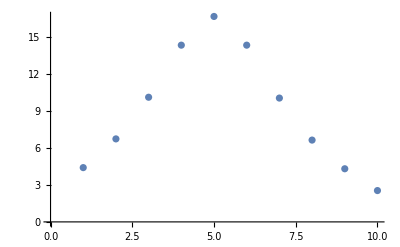

```mathematica
(*P1=Plot[nlm2[e],{e,emin,emax}];*)
ListPlot[Table[trafo[i+I],{i,1,10}]]
(*GraphicsGrid[{{P1,P2[Subscript[σ, i]]}}]
Plot[nlm2[e],{e,emin,emax}]*)
```